```mathematica
ToRodRule[rule_]:=Join[MapThread[Rule,{Join[Prepend[2]/@Tuples[{0,1},2],Tuples[{0,1},3],Append[2]/@Tuples[{0,1},2]],IntegerDigits[rule-1,2,16]}],{{2,2,0}->2,{2,2,1}->2,{0,2,2}->2,{1,2,2}->2}]
```

```mathematica
Length@ToRodRule[0]-4
```

16

```mathematica
(*RodEvolution[rule_,n_,t_,init_:Automatic]:=CellularAutomaton[ToRodRule[rule],Replace[init,Automatic->Join[{2},ConstantArray[0,n],{2}]],t]*)

RodEvolution2[rule_,init_]:=Last@CellularAutomaton[ToRodRule[rule],init,1]
```

{10}

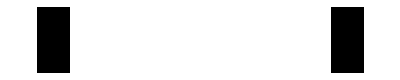

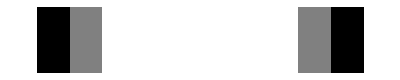

{11}

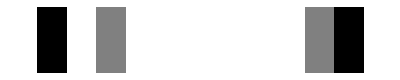

{11}

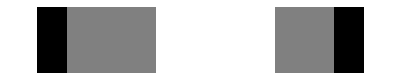

```mathematica
n=10;
start =Join[{2},RandomChoice[{0,1},n-2],{2}];
start = Join[{2},ConstantArray[0,n-2],{2}];
start//Dimensions
ArrayPlot[{start}]
update1 = RodEvolution2[50845,start];
ArrayPlot[{update1}]
grow1 = Join[{2,0},update1[[2;;-1]]]; (*Grow with a short state*)
grow1//Dimensions
ArrayPlot[{grow1}]
update2 = RodEvolution2[50845,grow1];
update2//Dimensions
ArrayPlot[{update2}]
```

```mathematica
IntegerDigits[50-1,2,16]
```

{0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1}

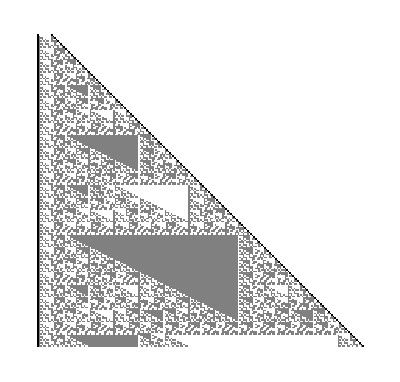

```mathematica
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,200];
ArrayPlot[updates]
```

```mathematica
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,2000];
ArrayPlot[updates]
```

-Graphics-

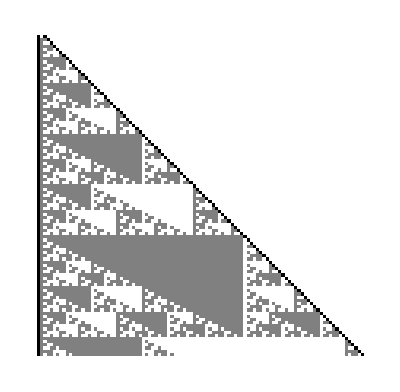

```mathematica
start={2,0,2};
updates =NestList[RodEvolution2[50845,Join[{2,0},#[[2;;-1]]]]&,start,100];
ArrayPlot[updates]
```

```mathematica
start={2,0,2};
numberofsamples = 10
ArrayPlot[#evol,PlotLabel->{#rule,#complexity}]&/@ReverseSortBy[Select[Table[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,200]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>],{rule,RandomInteger[2^16,numberofsamples]}],#complexity>1500&  ],#complexity&]
```

10

#### Find interesting ones with some constraints to help

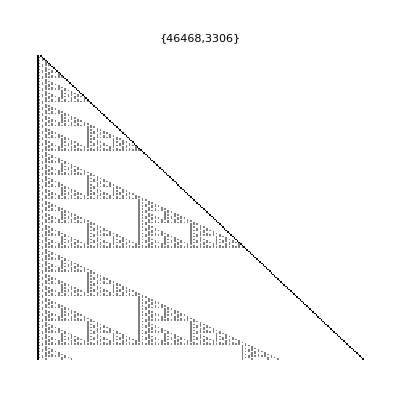
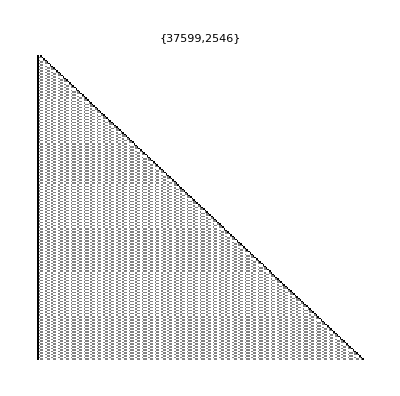
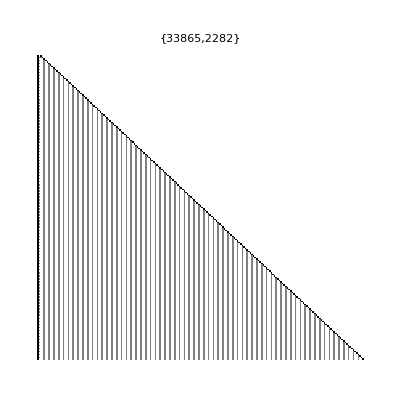
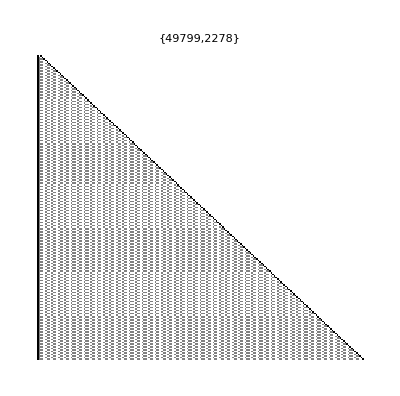
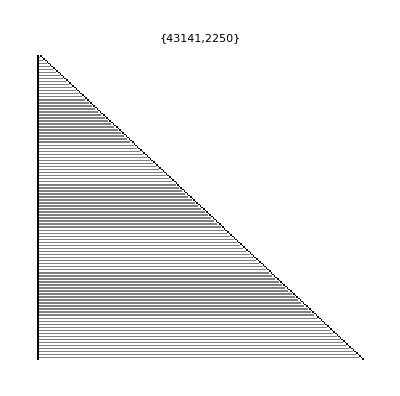
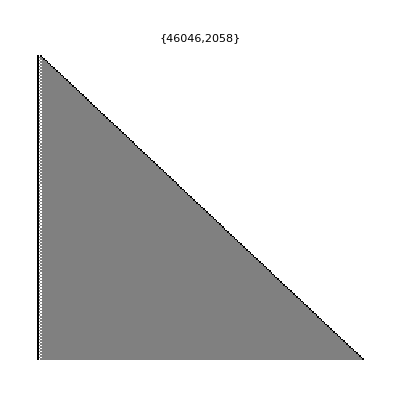
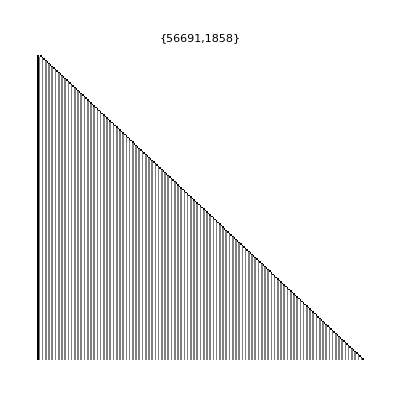
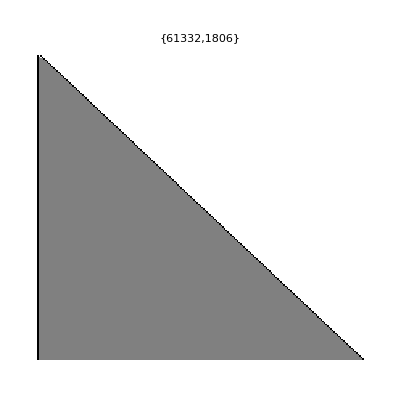

#### Have a look at interesting rules and select only a few that are dramatically different

```mathematica
i={1389,2671,2415,3612,2468,2883,5278,5278,6765,6984,10863,10516,10304,5279,14959,18283,51322,51864,54954,54251,33764,35241,35163,35306,38559,5305,39199,38971,42348,22188,22813,26475,26333,6910,41967,43884,46954,47944,47167,51051,51044,50152,50155,30700,31329,5803,34463,34667,60271,67437};
ii={1389,2671,2415,3612,2468,2883,5278,10516,10304,5279,14959,51322,51864,54954,54251,33764,35241,35163,35306,38559,5305,39199,38971,42348,22813,26475,26333,6910,41967,43884,46954,47944,47167,51051,51044,50152,30700,31329,5803,60271};
iii={46954,10304,22813,26475,33764,35306,51044,51051};
```

```mathematica
start={2,0,2};
numberofsamples = 10;
numberofevolutions = 4000;
var = 32;

all = Export["C:\\Users\\douwm\\repos\\wolfram_summer_school\\saved_results\\VeryLarge\\"<>ToString@#rule <>".png",ArrayPlot[#evol,PlotLabel->{#rule,#complexity}],ImageResolution->1000]&/@
ReverseSortBy[
Select[ParallelTable[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>],
{rule,iii}],
#complexity>5000 &&
1*numberofevolutions^2/2> Total[#evol,2]>2*numberofevolutions*2*1.3 &  ],#complexity&]
```

{C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\35241.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\42348.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\35163.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\5803.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\14959.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\2671.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\38559.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\31329.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\2415.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\3612.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\2468.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\51322.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\51864.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\54954.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\2883.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\5279.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\5278.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\26333.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\30700.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\47944.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\5305.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\43884.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\60271.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\51051.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\1389.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\26475.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\39199.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\35306.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\10516.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\51044.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\46954.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\22813.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\33764.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\10304.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\50152.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\54251.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\41967.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\38971.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\47167.png,C:\Users\douwm\repos\wolfram_summer_school\saved_results\Large\6910.png}

```mathematica
interesting = {10586,
33761,59817,39576,38571,26752,10581,38965,37861,18780,2396,31061,42858};
interestingdifferent = {10586,37861,39576,10581,42858};
randomish = {35177,38571};
```

```mathematica
start={2,0,2};
numberofsamples = 10;
numberofevolutions = 500;


ArrayPlot[#evol,PlotLabel->{#rule,#complexity}]&/@
Table[With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>],
{rule,randomish}]
```

{-Graphics-,-Graphics-}

#### Have a close look at 10586

```mathematica
rule = 10586;
numberofevolutions = 20000;


res =With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>];


ArrayPlot[#,PlotRange->{{1,All},{1,100}}]&/@Partition[PadRight[res["evol"]],numberofevolutions/10]
```

```mathematica
Row[ArrayPlot[#,PlotRange->{{1,All},{1,500}}]&/@Partition[PadRight[res["evol"]],numberofevolutions/10]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Have a close look at 37861

```mathematica
rule = 37861;
numberofevolutions = 20000;


res =With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>];


ArrayPlot[#,PlotRange->{{1,All},{1,All}}]&@PadRight[res["evol"]]
```

-Graphics-

#### Look at 42858

```mathematica
rule = 37861;
numberofevolutions = 2000;


res =With[{evol=NestList[RodEvolution2[rule,Join[{2,0},#[[2;;-1]]]]&,start,numberofevolutions]},<|"rule"->rule,"evol"->evol,"complexity"->StringLength@Compress[evol]|>];


ArrayPlot[#,PlotRange->{{1,All},{1,All}}]&@PadRight[res["evol"]]
```

-Graphics-